```mathematica
mFe=55.8/1000;(*/(6.022*10^23);*)
e=1.609*10^(-19);
Eg=14400*e;
c=2.998*10^8;
```

```mathematica
vFe[m_]=(m*c-Sqrt[(m*c)^2+m*Eg/2])/m;
EFe[m_]=1/2*m*((m*c-Sqrt[(m*c)^2+m*Eg/2])/m)^2/e;
R[m_]=Eg^2/(2*m*c^2)/e;
```

```mathematica
Clear[R,vFe,EFe]
```

```mathematica
dp=Eg/c;
dE=dp^2/(2*mFe)/e
```

0.00200306

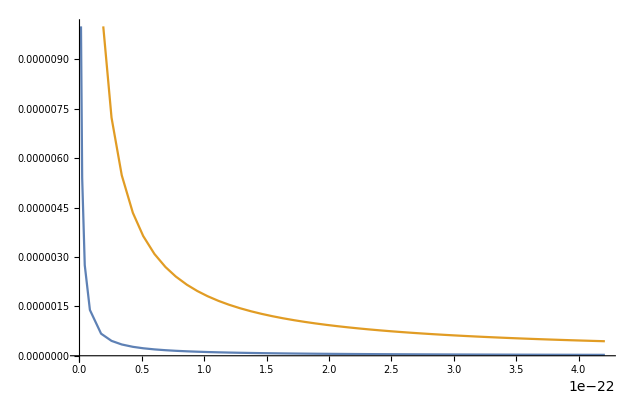

```mathematica
Plot[{EFe[m],R[m]},{m,55.8/1000/(6.626*10^23),55.8/1000/(6.626*10^23)*5000},PlotRange->{All,{0,0.00001}} ]
```